# SportifyMe

Visualization and statistical analysis of personal activity data using the Wolfram Language

Sabrina Kuhrn, Jun. 28,  2018

Sport is an important component in my life. Putting tracked activities into graphs and statistics sounds fun and interesting. Thus, let’s start with some basic statistical analysis and show some graphics afterwards.

## Data importing and first insights

Regarding  statistical analysis,  a spread sheet of data with basic information about activities was downloaded. Regarding visualization,  the same activities containing more detail  as longitude/latitude information etc. were exported individually .

```mathematica
spreadsheet=Import["projects/WSS2018/fit2Mathematica/Activities.csv",{"Dataset",All,Range[7]},"HeaderLines"->1,"Numeric"->True]
```

This gives the following table :

Dataset[<>]

Regarding the second part all activities (each of them saved as a separate CVS file ) were imported

```mathematica
targetDirectory=FileNameJoin[{$HomeDirectory,"projects","WSS2018","fit2Mathematica","Files"}]; 
(* set this to the directory that holds csv files *)
SetDirectory[targetDirectory];
filechoices=FileNames["*csv"]
```

{866G1518.csv,867I0011.csv,868I3006.csv,86AH5844.csv,86CG2839.csv,86CI1021.csv,86CI4402.csv,86D83833.csv,86F82554.csv,86FF1818.csv,86FG1858.csv,86H82942.csv,86JI0018.csv,86K70839.csv,86L64651.csv,86ND4622.csv,86O84356.csv,86Q62948.csv}

and saved as a list :

```mathematica
AllCsv=Import[#,{"Data"},"HeaderLines"->1,"Numeric"->True]&/@filechoices
```

{{{2018-06-06 09:15:18-05:00,48.2048,16.4198,0.00067,158.6,158.6,2.1168,2.1168,67,60,0.},{2018-06-06 09:15:19-05:00,48.2048,16.4198,0.00139,158.4,158.4,5.3748,5.3748,64,60,0.},518,{2018-06-06 10:01:59-05:00,48.2044,16.4226,8.61258,171.4,171.4,11.052,11.052,152,85,0.5}},{1},14,{1},{1}}
 |  |  |  |

When inspecting the loaded dataset, it looks as both activity types, cycling and running, are distributed equally. Observing  the different activity attributes someone can see that the heart rate is higher for running whereas the covered distance is much less compared to cycling. Calories seems to be correlated to Distance and somehow to Time when focusing on one activity type. As the Wolfram Language offers powerful tools to do statistical analysis, let’s proof the assumptions made.

## Statistical Analysis

A BarChart is used to underline the first assumption and show that both activities are practiced equally.

```mathematica
hist=Tally[spreadsheet[[All,"Activity Type"]]];
label=hist[[All,1]]//Normal;
BarChart[hist[[All,2]],ChartStyle->"Pastel",ChartLabels->label]
```

This results in :

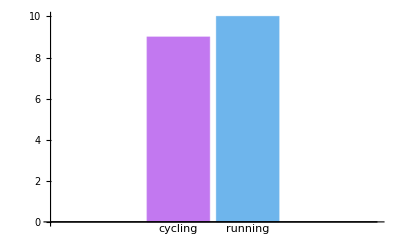

To proof if the other assumptions are correct too, we do some further statistical analysis. Looking at the overall average heart rate and comparing it to the average heart rate of both activity types,  proofs again the assumptions made. Considering my data are correct and do not include outlier someone can see that the heart rate is slightly higher on average.

Overall heart rate:

```mathematica
N@Mean[spreadsheet[[All,"Avg HR"]]]
```

147.105

Grouped by activity type:

```mathematica
spreadsheet[GroupBy["Activity Type"],All,"Avg HR"][All,Mean]
```

Dataset[<>]

Tracking your heart rate  tells you precisely how hard—or easy—your heart is working. One would say that for an athletic person the average heart rate is quite high here and would suggest that the training is too hard and intense.

Regarding experts' opinion someone should always workout in specific heart zones, which are calculated based on your maximum heart rate (MHR).  The equation which is the most common one is

220 – age = MHR.

This would mean that my MHR equals 193. As most of the training should fall in Zone 1 and 2 meaning 60 to 80% of the MHR, the heart  in our case should be between 115 and 155 most of the time. Regarding running activities that would mean that the training is most of the time in the upper region of Zone 2.  Thus, let’s look at the maximum heart rate of the tracked activities and see if the MHR is maybe higher than the above calculated one.

Looking at the table above and calculating the maximum of the "Max HR"  column shows that my MHR is above the estimated MHR:

```mathematica
N@Max[spreadsheet[[All,"Max HR"]]]
```

207.

Of course that could be an outlier too. So let’s calculate the mean of the “Max HR” column:

```mathematica
N@Mean[spreadsheet[[All,"Max HR"]]]
```

172.842

Which is pretty high too if someone imagine that the data do not include any competition activities.  Now most experts agree that the formula above may be inaccurate for most people. It  is better to monitor your heart rate based on something known as heart rate reserve (HRR), which is more accurate and can be calculated by taking the MHR of a 5-K race (there you will likely be able to sustain about 97% of your max heart rate ), getting your resting heart rate (RHR) too, which can be retrieved by monitoring your heart rate as soon as you wake up by counting your pulse for a full 60 seconds and repeat this for a few days.  In the end, the HRR is the MHR minus the RHR.

Regarding this purpose we will import some information about a 5-K run I did last year extract the MHR from this specific run:

```mathematica
Import["projects/WSS2018/fit2Mathematica/5k.csv",{"Dataset",All,{4,13,14}},"HeaderLines"->1,"Numeric"->True][[6]]
```

Dataset[<>]

The MHR  regarding the 5-K is 208 and as I know my RHR, which is about 45, we can now easily calculate the RHR:

```mathematica
Solve[208==0.97*MHR ,MHR];
MHR-45/.%
```

{169.433}

To find out now which numbers to target on which runs, multiply the HRR by the zone you want to run in and add back your resting heart rate.

Thus, running somewhere in Zone 1 and 2 (let's say 65%) would give the following heart rate:

```mathematica
%*0.65+45
```

{155.131}

This result looks a way better as it is totally in line with the average running heart rate calculated above.

Enough investigations done on heart rate now, so let’s go back to basic statistical analysis and focusing on covered distance now.

Again calculating the mean of covered distance gives on overall level:

20.09

Grouped by activity type:

Dataset[<>]

Again the made assumption seems to be correct. This absolutely makes sense, as in general more distance is covered by cycling than by running if someone is not into ultra running, which I am definitely not.

Finally, calculate at the correlation of “Distance” and “Calories” :

```mathematica
Correlation[spreadsheet[[All,"Distance"]]//Normal,spreadsheet[[All,"Calories"]]//Normal]
```

0.399699

So the correlation is not that high but a weak relationship can be seen.

As a lot statistics can be done with the Wolfram Language, more are shown in the next subsection.

### More Statistics

Visualizing the distribution of the covered distance by plotting histograms for the PDF and CDF:

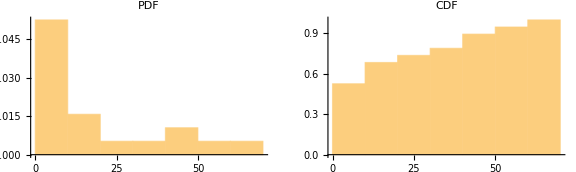

```mathematica
GraphicsRow[{histplotpdf,histplotcdf}={Histogram[spreadsheet[[All,"Distance"]],10,"PDF",PlotLabel->"PDF"],Histogram[spreadsheet[[All,"Distance"]],10,"CDF",PlotLabel->"CDF"]},ImageSize-> Large]
```

As Wolfram Language also offers to fit the data to a known parametric distribution using FindDistribution let us try this for the distance data visualized above.

Find the underlying distribution of the data

```mathematica
Subscript[𝒟, p]=FindDistribution[spreadsheet[[All,"Distance"]]]
```

MixtureDistribution[{0.660698,0.339302},{NormalDistribution[6.76586,3.29445],NormalDistribution[50.4869,15.773]}]

and see how good it fits:

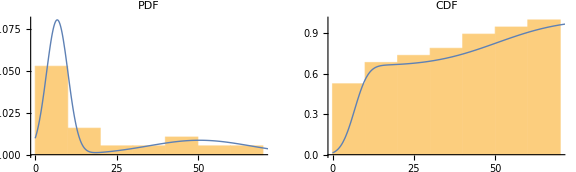

```mathematica
GraphicsRow[{Show[{
histplotpdf,
estplot= Plot[PDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick,PlotRange->{0,0.8}]
}],Show[{
histplotcdf,
estplot= Plot[CDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick]}
]},ImageSize-> Large]
```

This looks very reasonable as someone can see two “peaks” regarding the PDF, one regarding running activities and one regarding cycling.

Since having found an underlying distribution let’s calculate how likely I cover a distance of more than twelve kilometers.

```mathematica
Probability[x>12.0,x\[Distributed] Subscript[𝒟, p]]
```

0.373846

That probability is low but again reasonable as  most of the time I am running between five and ten kilometers. Moreover, I did some short cycling tours too.  For now enough statistical analysis was done, so let’s focus on visualization in the second part.

## Visualization of activity data

The Wolfram Language offers many tools for data visualization. A few will be shown in this section below.

The second part of imported data files is used and an overview of covered routes is plotted:

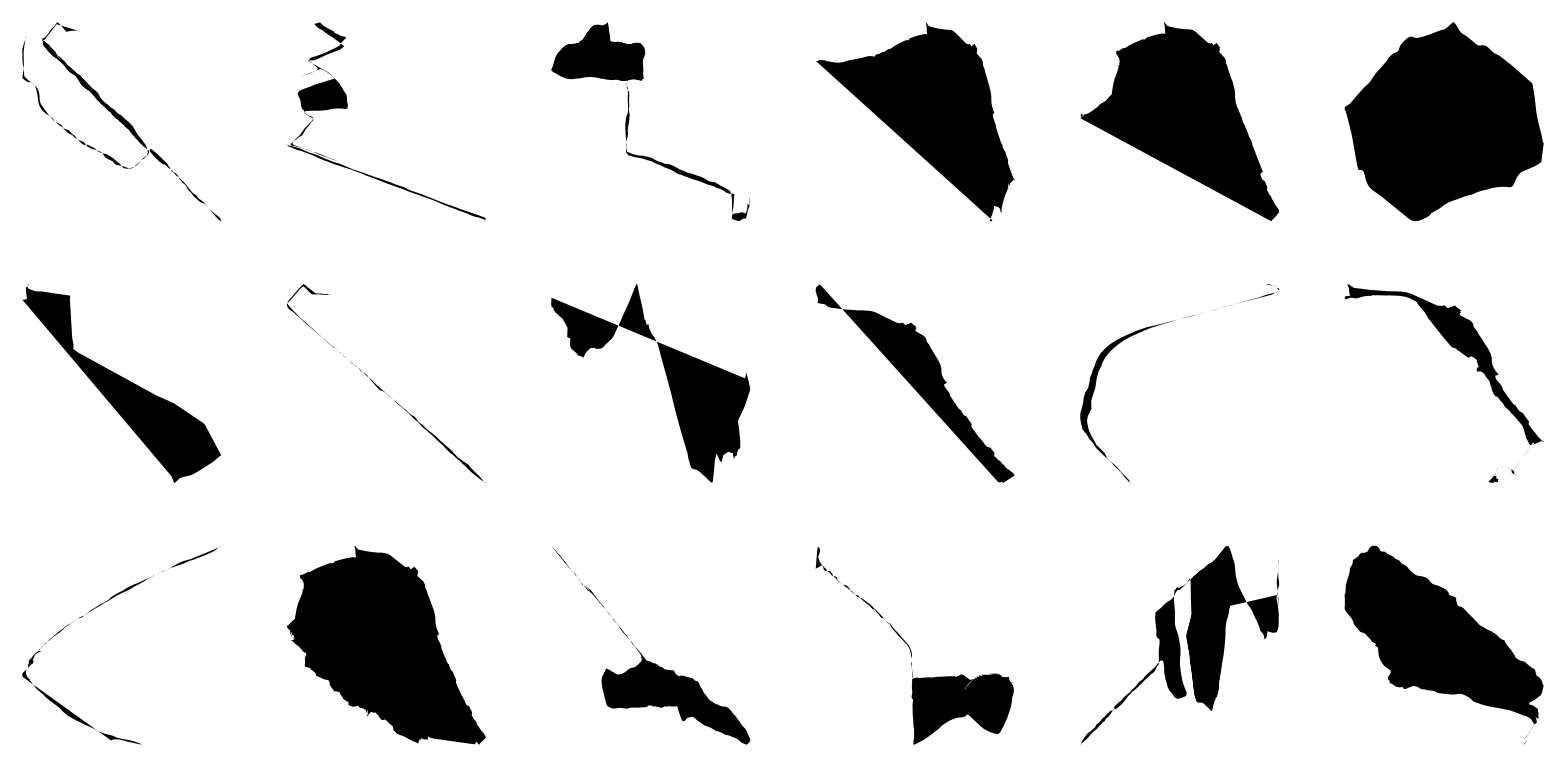

```mathematica
AllLatLong=Map[Reverse,#[[All,{3,2}]]&]/@AllCsv;
GraphicsGrid[Partition[Graphics[Polygon[#]]&/@AllLatLong,6]]
```

These are the route of running and cycling activities done in the last month. Someone can easily differentiate the running and cycling routes as the latter cover a bigger area. Not obvious but at least I know, the last graphic of the plot shows the route of the cycling tour done in Waltham, Massachusetts.

Let’s do some analysis on this tour and show some nice visualization tools.

Therefore, the CSV file of the cycling activity gets imported

```mathematica
choicePathAndName=StringReplace[FileNameJoin[Flatten[{targetDirectory,filechoices[[choiceNumber]]}]]," "->"\\ "];
inFit=Import[choicePathAndName,{"Data"},"HeaderLines"->1,"Numeric"->True]
```

{{2018-06-26 05:29:48-05:00,42.3881,-71.2217,0.,36.2,36.2,10.6812,10.6812,88,,},1189,{2018-06-26 07:32:00-05:00,42.3865,-71.2231,49.289,50.4,50.4,0.,0.,126,,}}
 |  |  |  |

and visualized in a few nice ways:

```mathematica
latLongAlt=inFit[[All,{3,2,6}]];
latLongSpeed=inFit[[All,{3,2,8}]];
altplot=ListPointPlot3D[latLongAlt,Filling->None,BoxRatios->{Automatic,Automatic,.04},
		ColorFunction->(ColorData["Rainbow",2.5 (#3-0.6)]&),AxesLabel->{"latitude","longitude","altitude"},ImageSize->Large];
speedplot=ListPointPlot3D[latLongSpeed,Filling->Bottom,BoxRatios->{Automatic,Automatic,.04},
		ColorFunction->(ColorData[{"SunsetColors","Reverse"}][#3]&),AxesLabel->{"latitude","longitude","speed"},ImageSize->Large];
Show[altplot,speedplot]
```

-Graphics3D-

Someone can see that if it is going down, the speed is getting higher.  Nice to look at, but as nobody knows the route  direction (except me) and going up or down depends on that the before mentioned negative correlation cannot be seen immediately.

Therefore, an interactive map is plotted by using Manipulate:

```mathematica
Manipulate[
		GeoGraphics[GeoPath[Take[inFit[[All,{2,3}]],UpTo[Floor[pointsToShow]]]],
		GeoRange->{{42.3793710465543,42.53642104798928},{-71.38013072591275,-71.1983386958018}}
		],{{pointsToShow,Length[latLong],"Cycling distance"},0,Length[latLong],
	AnimationRate->inFit[[All,8]][[pointsToShow]],AnimationDirection->Forward},SaveDefinitions->True]
```

Someone can see that the Wolfram Language offers many useful tools when it comes to analyse data, both for statistics and also for visualization purpose.

## Further explorations

Analysing more activity data from history, moreover getting data from other athletes too would be great to do even more statistical analysis.

## Author contact information

sabrina.kuhrn@gmx.at